Método de Newton (Diferencias divididas)

### Helver Jussef López Abril Michael Velasquez Rico

Consiste en escribir el polinomio de interpolación en la forma :

```mathematica
p(x)= Subscript[A, 0]+Subscript[A, 1](x-Subscript[x, 0])+Subscript[A, 2](x-Subscript[x, 0])(x-Subscript[x, 1])+....+Subscript[A, n-1](x-Subscript[x, 0])(x-Subscript[x, 1])...(x-Subscript[x, n-1])
```

#### Ejemplo:

Calcular el polinomio que interpola al conjunto de datos:

{(8,4),(-2,5),(4,6),(3,2),(6,0),(8,-3),}

```mathematica
puntos={{-5,1},{-3,2},{2,10},{3,2},{6,0},{8,-3}};
```

```mathematica
n=Length[puntos]-1;
```

```mathematica
For[i=0,i≤n,i++,Subscript[x, i]=puntos[[i+1,1]];Subscript[f, i]=puntos[[i+1,2]]]
```

```mathematica
Clear[d];
dif=Array[d,{2n+2,n+2},-1];
```

```mathematica
For[i=-1,i≤2n,i++,For[j=-1,j≤n,j++,d[i,j]= " "]]
```

```mathematica
d[-1,-1]= "x_k";d[-1,0]="f_k";For[i=0,i≤n+1,i++,d[2i,-1]=Subscript[x, i];d[2i,0]=Subscript[f, i]];
```

```mathematica
dif // MatrixForm
```

(x_k | f_k |   |   |   |   |  
-5 | 1 |   |   |   |   |  
  |   |   |   |   |   |  
-3 | 2 |   |   |   |   |  
  |   |   |   |   |   |  
2 | 10 |   |   |   |   |  
  |   |   |   |   |   |  
3 | 2 |   |   |   |   |  
  |   |   |   |   |   |  
6 | 0 |   |   |   |   |  
  |   |   |   |   |   |  
8 | -3 |   |   |   |   |  )

```mathematica
For[j=1,j≤n,j++,For[i=j,i≤2n-j,i=i+2,d[i,j]=(d[i+1,j-1]-d[i-1,j-1])/(d[i+j,-1]-d[i-j,-1])]]
```

```mathematica
dif // MatrixForm
```

(x_k | f_k |   |   |   |   |  
-5 | 1 |   |   |   |   |  
  |   | 1/2 |   |   |   |  
-3 | 2 |   | 11/70 |   |   |  
  |   | 8/5 |   | -123/560 |   |  
2 | 10 |   | -8/5 |   | 9089/166320 |  
  |   | -8 |   | 103/270 |   | -19897/2162160
3 | 2 |   | 11/6 |   | -193/2970 |  
  |   | -2/3 |   | -1/3 |   |  
6 | 0 |   | -1/6 |   |   |  
  |   | -3/2 |   |   |   |  
8 | -3 |   |   |   |   |  )

```mathematica
PolinomioSolucion=∑_(k=0)^n d[k,k](∏_(j=0)^(k-1) (x-Subscript[x, j]))
```

1+(5+x)/2+11/70 (3+x) (5+x)-123/560 (-2+x) (3+x) (5+x)+(9089 (-3+x) (-2+x) (3+x) (5+x))/166320-(19897 (-6+x) (-3+x) (-2+x) (3+x) (5+x))/2162160

```mathematica
Expand[PolinomioSolucion]
```

67069/3003-(109171 x)/60060-(810709 x^2)/270270+(615757 x^3)/2162160+(2021 x^4)/24570-(19897 x^5)/2162160

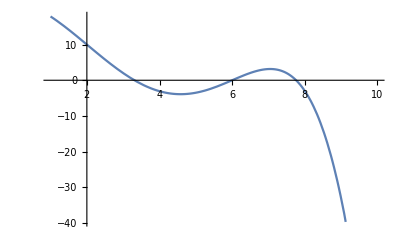

```mathematica
Plot[67069/3003-(109171 x)/60060-(810709 x^2)/270270+(615757 x^3)/2162160+(2021 x^4)/24570-(19897 x^5)/2162160,{x,1,10}]
```